```mathematica
r1=100;
r2=0;
r3=-100;
min=10^-6;
```

```mathematica
m=5/2;
λ=π/2;
```

```mathematica
sol3=ParametricNDSolve[{-f''[x]/(2m)+λ Abs[x]f[x]-f''''[x]/(32 m^3)==e f[x],f'''[r1]==-min,f'[r1]==-min,f'[r2]==min,f''[r1]==min},f,{x,r3,r1},e,MaxSteps->Infinity]
FindRoot[f[e][r1]==min/.sol3,{e,0.4,0.9}]
```

{f→ParametricFunction[<>]}

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

ParametricNDSolve::berr: 3.43307431030495×10^490 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

ParametricNDSolve::berr: 1.91258902735895×10^489 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

General::stop: 在本次计算中，ParametricNDSolve::bvluc 的进一步输出将被抑制.

ParametricNDSolve::berr: 1.91258902735895×10^489 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

General::stop: 在本次计算中，ParametricNDSolve::berr 的进一步输出将被抑制.

```mathematica
sol4=ParametricNDSolve[{-f''[x]/(2m)+λ Abs[x]f[x]-(e-λ Abs[x])^2/(8m)f[x]==e f[x],f'[r1]==-min,f'[r2]==min},f,{x,r2,r1},e,MaxSteps->Infinity(*,WorkingPrecision->30,PrecisionGoal->20*)]
```

{f→ParametricFunction[<>]}

```mathematica
FindRoot[f[e][r1]==min/.sol4,{e,0.75,0.799}]
```

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

ParametricNDSolve::berr: 9.3547×10^9 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

ParametricNDSolve::ndsz: 在 x == 73.2767 处，步长实际上为零；可能存在奇点或者刚性系统.

InterpolatingFunction::dmval: 输入值 {100} 位于插值函数的数据范围之外. 将使用外推法.

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

ParametricNDSolve::berr: 2.42521×10^12 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

General::stop: 在本次计算中，ParametricNDSolve::bvluc 的进一步输出将被抑制.

ParametricNDSolve::berr: 9.29862×10^9 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

General::stop: 在本次计算中，ParametricNDSolve::berr 的进一步输出将被抑制.

ParametricNDSolve::ndsz: 在 x == 86.4727 处，步长实际上为零；可能存在奇点或者刚性系统.

InterpolatingFunction::dmval: 输入值 {100} 位于插值函数的数据范围之外. 将使用外推法.

ParametricNDSolve::ndsz: 在 x$12758 == 98.2894 处，步长实际上为零；可能存在奇点或者刚性系统.

General::stop: 在本次计算中，ParametricNDSolve::ndsz 的进一步输出将被抑制.

InterpolatingFunction::dmval: 输入值 {100} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

{e→0.75}

```mathematica
FindRoot[f[e][r1]==min/.sol4,{e,0.7,0.8}]
```

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

ParametricNDSolve::berr: 1.46228×10^9 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

ParametricNDSolve::berr: 2.05607×10^10 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

General::stop: 在本次计算中，ParametricNDSolve::bvluc 的进一步输出将被抑制.

ParametricNDSolve::berr: 5.30072×10^9 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

General::stop: 在本次计算中，ParametricNDSolve::berr 的进一步输出将被抑制.

ParametricNDSolve::ndsz: 在 x == 75.0403 处，步长实际上为零；可能存在奇点或者刚性系统.

InterpolatingFunction::dmval: 输入值 {100} 位于插值函数的数据范围之外. 将使用外推法.

ParametricNDSolve::ndsz: 在 x == 94.456 处，步长实际上为零；可能存在奇点或者刚性系统.

InterpolatingFunction::dmval: 输入值 {100} 位于插值函数的数据范围之外. 将使用外推法.

ParametricNDSolve::ndsz: 在 x == 94.7302 处，步长实际上为零；可能存在奇点或者刚性系统.

General::stop: 在本次计算中，ParametricNDSolve::ndsz 的进一步输出将被抑制.

InterpolatingFunction::dmval: 输入值 {100} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

{e→0.708083}

```mathematica
FindRoot[f[e][r1]==min/.sol4,{e,2.3,2.5}]
```

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

ParametricNDSolve::berr: 1.20756×10^9 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

ParametricNDSolve::berr: 1.55779×10^11 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

General::stop: 在本次计算中，ParametricNDSolve::bvluc 的进一步输出将被抑制.

ParametricNDSolve::berr: 1.55779×10^11 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

General::stop: 在本次计算中，ParametricNDSolve::berr 的进一步输出将被抑制.

ParametricNDSolve::ndsz: 在 x == 82.323 处，步长实际上为零；可能存在奇点或者刚性系统.

InterpolatingFunction::dmval: 输入值 {100} 位于插值函数的数据范围之外. 将使用外推法.

ParametricNDSolve::ndsz: 在 x$12758 == 79.2915 处，步长实际上为零；可能存在奇点或者刚性系统.

{e→2.50289}

```mathematica
FindRoot[f[e][r1]==min/.sol4,{e,2.4,2.6}]
```

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

ParametricNDSolve::berr: 2.60084×10^10 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

ParametricNDSolve::berr: 1.12092×10^9 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

General::stop: 在本次计算中，ParametricNDSolve::bvluc 的进一步输出将被抑制.

ParametricNDSolve::berr: 1.91701×10^10 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

General::stop: 在本次计算中，ParametricNDSolve::berr 的进一步输出将被抑制.

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

{e→2.56503}

```mathematica
(2.5650290434564527 -2.32744)/2.32744
```

0.102082

```mathematica
FindRoot[f[e][r1]==min/.sol4,{e,0.7,0.8},WorkingPrecision->20,PrecisionGoal->8]
```

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

ParametricNDSolve::berr: 1.46228×10^9 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

ParametricNDSolve::berr: 2.05607×10^10 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

General::stop: 在本次计算中，ParametricNDSolve::bvluc 的进一步输出将被抑制.

ParametricNDSolve::berr: 5.30072×10^9 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

General::stop: 在本次计算中，ParametricNDSolve::berr 的进一步输出将被抑制.

ParametricNDSolve::ndsz: 在 x == 75.0403 处，步长实际上为零；可能存在奇点或者刚性系统.

InterpolatingFunction::dmval: 输入值 {100} 位于插值函数的数据范围之外. 将使用外推法.

ParametricNDSolve::ndsz: 在 x == 75.0403 处，步长实际上为零；可能存在奇点或者刚性系统.

InterpolatingFunction::dmval: 输入值 {100} 位于插值函数的数据范围之外. 将使用外推法.

ParametricNDSolve::ndsz: 在 x$138724 == 19.503 处，步长实际上为零；可能存在奇点或者刚性系统.

General::stop: 在本次计算中，ParametricNDSolve::ndsz 的进一步输出将被抑制.

InterpolatingFunction::dmval: 输入值 {100} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

FindRoot::brdig: 根已经被 20. 工作数位紧密包围，但是函数值超过了绝对容差 1.×10^-10.

{e→0.70796017340807265713}

```mathematica
FindRoot[f[e][r1]==min/.sol4,{e,0.4,0.9},WorkingPrecision->20,PrecisionGoal->8]
```

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

ParametricNDSolve::berr: 1.73751×10^7 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

ParametricNDSolve::berr: 2.37956×10^9 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

General::stop: 在本次计算中，ParametricNDSolve::bvluc 的进一步输出将被抑制.

ParametricNDSolve::berr: 1.73751×10^7 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

General::stop: 在本次计算中，ParametricNDSolve::berr 的进一步输出将被抑制.

ParametricNDSolve::ndsz: 在 x$138724 == 97.2839 处，步长实际上为零；可能存在奇点或者刚性系统.

ParametricNDSolve::ndsz: 在 x$138724 == 71.1993 处，步长实际上为零；可能存在奇点或者刚性系统.

{e→3.6569740602971061022}

```mathematica
FindRoot[f[e][r1]==min/.sol4,{e,2.2,2.6},WorkingPrecision->20,PrecisionGoal->8]
```

FindRoot::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

{e→2.5946570949316210771}

```mathematica
FindRoot[f[e][r1]==min/.sol4,{e,2.4,2.7},WorkingPrecision->20,PrecisionGoal->8]
```

FindRoot::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

{e→2.7295643417550762657}

```mathematica
FindRoot[f[e][r1]==min/.sol4,{e,2.9,3.4},WorkingPrecision->20,PrecisionGoal->8]
```

FindRoot::brdig: 根已经被 20. 工作数位紧密包围，但是函数值超过了绝对容差 1.×10^-10.

{e→3.338224629721081138}

```mathematica
FindRoot[f[e][r1]==min/.sol4,{e,3.1,3.5},WorkingPrecision->20,PrecisionGoal->8]
```

FindRoot::brdig: 根已经被 20. 工作数位紧密包围，但是函数值超过了绝对容差 1.×10^-10.

{e→3.4061435793144700935}

```mathematica
FindRoot[f[e][r1]==min/.sol4,{e,2.6,3},WorkingPrecision->20,PrecisionGoal->8]
```

FindRoot::brdig: 根已经被 20. 工作数位紧密包围，但是函数值超过了绝对容差 1.×10^-10.

{e→2.7295661954110006508}

```mathematica
FindRoot[f[e][r1]==min/.sol4,{e,3.43,3.9}]
```

{e→3.61022}

```mathematica
FindRoot[f[e][r1]==min/.sol4,{e,3.5,3.7},WorkingPrecision->20,PrecisionGoal->8]
```

FindRoot::brdig: 根已经被 20. 工作数位紧密包围，但是函数值超过了绝对容差 1.×10^-10.

{e→3.6783783600089174916}

```mathematica
FindRoot[f[e][r1]==min/.sol4,{e,3.43,3.9},WorkingPrecision->20,PrecisionGoal->8]
```

FindRoot::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

{e→322.93268653007078731}

```mathematica
FindRoot[f[e][r1]==min/.sol4,{e,2.5},WorkingPrecision->20,PrecisionGoal->8]
```

{e→2.3862623275058896334}

```mathematica
FindRoot[f[e][r1]==min/.sol4,{e,4,4.6}]
```

{e→5.19502}

```mathematica
FindRoot[f[e][r1]==min/.sol4,{e,3.9,4.1}]
```

{e→3.95109}

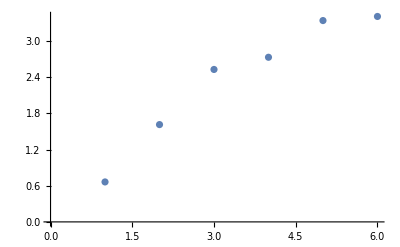

```mathematica
ListPlot@{0.662478,1.61335,2.52748,2.72957,3.33822,3.40614}
```

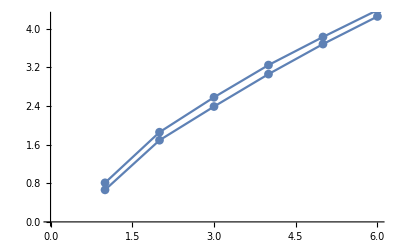

```mathematica
Show[ListPlot[{0.662478,1.68939,2.38626,3.057,3.67838,4.25},Joined->True,PlotMarkers->Automatic],ListPlot[{0.8086165174976805,1.8557570815563174,2.5780961296407856,3.244607624290441,3.825715279680601,4.38167123996999},Joined->True,PlotMarkers->Automatic]]
```